```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]]; 
Needs["ErrorBarPlots`"];
Needs["NumericalCalculus`"];
```

### HRG- AltExS

## HRG w/ Repulsive

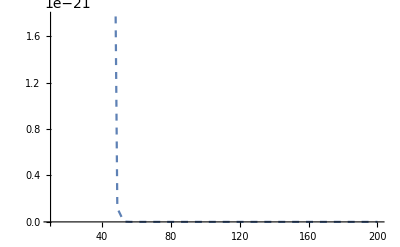

```mathematica
Plot[BesselK[2,x],{x,10,200},PlotStyle->Dashed, PlotLegends->Automatic]
```

## VdW HRG

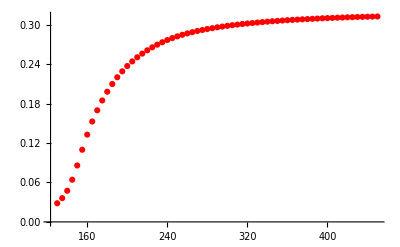

```mathematica
chi4l=Import["/Users/michaeladmin/Desktop/HRG-AltExS/Lattice/chi4.dat"];
chi2La = Import["/Users/michaeladmin/Desktop/HRG-AltExS/Lattice/2102.06660/chiB2.dat"];
chi2Lat = Table[{chi2La[[i,1]],chi2La[[i,2]],chi2La[[i,3]],chi2La[[i,4]],chi2La[[i,5]]},{i,2,Length[chi2La]}];
ErrorListPlot[chi2Lat[[All,{1,2,3}]], PlotStyle->Red]
```

### Particle list

```mathematica
(*Clears the comment lines as well as the Gamma particle from the list, if any*)
CleanTheParticleList[list_]:=Module[{ret={}},
Do[
If[StringPart[ToString[list[[i,1]]],1]=="#" || list[[i,1]]==22,Continue[]];
AppendTo[ret,list[[i]]];
,
{i,1,list//Length}];
ret
];
(*The PDG2020 list, modify as needed*)
hadrons=Import[StringJoin[NotebookDirectory[],"PDG2016PlusThFIST.dat"]];
hadrons=CleanTheParticleList[hadrons];
(*Data=Import["/Users/michaeladmin/Desktop/HRG-AltExS/PDG21Plus_ThFIST.dat"];*)(*PDG2021plus *)(* colomn 3: stable ,colomn 4: mass[GeV], colomn 5: degeneracy,  colomn 6: statistics, colomn 7: B, colomn 8: Q,  colomn 9: S .............*)
phi[T_,m_] = m^2*T/(2*π^2)*BesselK[2,m/T];
PHIBaryon[T_]:= Sum[If[hadrons[[i]][[7]]==1,hadrons[[i]][[5]]*phi[T,hadrons[[i]][[4]]*1000],0],{i,1,Length[hadrons]}];
```

```mathematica
(*Define parameters*)
  b = 3.42*(1/197.3)^3;(*MeV^-3*)
 a=329*(1/197.3)^3;(*MeV^-2*)
```

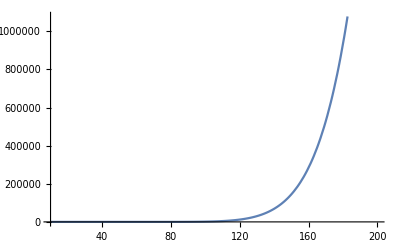

```mathematica
Plot[PHIBaryon[T],{T,10,200}]
```

```mathematica
nBB[T_,muB_,a_,b_]:= If[a==0&&b==0,PHIBaryon[T]*Exp[muB/T],FindRoot[nBr/(PHIBaryon[T]*(1-nBr*b))*Exp[(b*nBr)/(1-b*nBr)-(2*a*nBr)/T] ==Exp[muB/T],{nBr,50000}][[1,2]]];
nAB[T_,muB_,a_,b_]:= If[a==0&&b==0,PHIBaryon[T]*Exp[-muB/T],FindRoot[nBr/(PHIBaryon[T]*(1-nBr*b))*Exp[(b*nBr)/(1-b*nBr)-(2*a*nBr)/T] ==Exp[-muB/T],{nBr,50000}][[1,2]]];
nBDensity[T_,muB_,a_,b_]:=(nBB[T,muB,a,b] - nAB[T,muB,a,b]) ;
Bardenfull[T_,muB_,a_,b_]:=nBDensity[T,muB,a,b]/T^3;
```

```mathematica
Plot3D[Bardenfull[T,muB,0,0],{muB,0,700},{T,10,200}]
```

-Graphics3D-

## Lattice chis/kappa

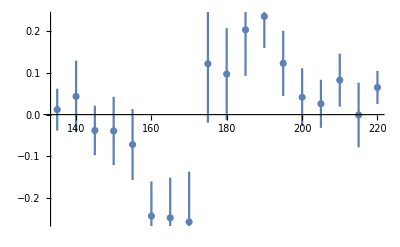

```mathematica
chis = Import["/Users/michaeladmin/Desktop/HRG-AltExS/lqcd/WB-chiB-1805.04445.dat"];
chiss = Table[{chis[[i,1]],chis[[i,2]],chis[[i,3]],chis[[i,4]],chis[[i,5]],chis[[i,6]],chis[[i,7]],chis[[i,8]],chis[[i,9]]},{i,2,Length[chis]}];
 ErrorListPlot[chiss[[All,{1,8,9}]]]
```

```mathematica
Kappa = Import["/Users/michaeladmin/Desktop/HRG-AltExS/Lattice/2102.06660/kappa_all.dat"];
KappaLat = Table[{Kappa[[i,1]],Kappa[[i,2]],Kappa[[i,3]],Kappa[[i,4]],Kappa[[i,5]]},{i,2,Length[Kappa]}];
```

## Numerical Derivative/ Chis

```mathematica
diff=0.1;
dnBDensitydT[T_,muB_,a_,b_]:=(nBDensity[T-2*diff,muB,a,b]-8*nBDensity[T-diff,muB,a,b]+8*nBDensity[T+diff,muB,a,b]-nBDensity[T+2*diff,muB,a,b])/(12*diff);
chi2HrgN[T_,muB_,a_,b_]:=T*(nBDensity[T,muB-2*diff,a,b]-8*nBDensity[T,muB-diff,a,b]+8*nBDensity[T,muB+diff,a,b]-nBDensity[T,muB+2*diff,a,b])/(12*diff);
chi3HrgN[T_,muB_,a_,b_]:=T^2*(-nBDensity[T,muB-2*diff,a,b]+16*nBDensity[T,muB-diff,a,b]-30*nBDensity[T,muB,a,b]+16*nBDensity[T,muB+diff,a,b]-nBDensity[T,muB+2*diff,a,b])/(12*diff^2);
dchi2HrgdTN[T_,muB_,a_,b_]:=(chi2HrgN[T-2*diff,muB,a,b]-8*chi2HrgN[T-diff,muB,a,b]+8*chi2HrgN[T+diff,muB,a,b]-chi2HrgN[T+2*diff,muB,a,b])/(12*diff);
d2chi2HrgdT2N[T_,muB_,a_,b_]:=(2*chi2HrgN[T-3*diff,muB,a,b]-27*chi2HrgN[T-2*diff,muB,a,b]+270*chi2HrgN[T-diff,muB,a,b]-490*chi2HrgN[T,muB,a,b]+270*chi2HrgN[T+diff,muB,a,b]-27*chi2HrgN[T+2*diff,muB,a,b]+2*chi2HrgN[T+3*diff,muB,a,b])/(180*diff^2);
chi4HrgN[T_,muB_,a_,b_]:=T^3*(nBDensity[T,muB-3*diff,a,b]-8*nBDensity[T,muB-2*diff,a,b]+13*nBDensity[T,muB-diff,a,b]-13*nBDensity[T,muB+diff,a,b]+8*nBDensity[T,muB+2*diff,a,b]+-nBDensity[T,muB+3*diff,a,b])/(8*diff^3);
chi5HrgN[T_,muB_,a_,b_]:=T^4*(7*nBDensity[T,muB-4*diff,a,b]-96*nBDensity[T,muB-3*diff,a,b] +676*nBDensity[T,muB-2*diff,a,b]-1952*nBDensity[T,muB-diff,a,b]+2730*nBDensity[T,muB,a,b]-1952*nBDensity[T,muB+diff,a,b]+676*nBDensity[T,muB+2*diff,a,b]-96*nBDensity[T,muB+3*diff,a,b]+7*nBDensity[T,muB+4*diff])/(240*diff^4);
chi6HrgN[T_,muB_,a_,b_]:=T^5*(-13*nBDensity[T,muB-5*diff,a,b]+152nBDensity[T,muB-4*diff,a,b]-783*nBDensity[T,muB-3*diff,a,b]+1872*nBDensity[T,muB-2*diff,a,b]-1938*nBDensity[T,muB-diff,a,b]+1938*nBDensity[T,muB+diff,a,b]-1872*nBDensity[T,muB+2*diff,a,b]+783*nBDensity[T,muB+3*diff,a,b]-152*nBDensity[T,muB+4*diff,a,b] + 13*nBDensity[T,muB+5*diff,a,b])/(288*diff^5);
```

## Analytic Derivative/ Chis

```mathematica
(*ch2hrgA[T_,muB_,a_,b_]:=Module[{Bnden,result},Bnden=nBB[T,muB,a,b];
result=(Bnden*(1/(1-b*Bnden)^2-(2*a*Bnden)/T)^-1);
result];
ch3hrgA[T_,muB_,a_,b_]:=Module[{ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];
result=((-1+b*Bnden)*(-1+3*b*Bnden)*ch2nden*T^2)/((-2*a*Bnden+4*a*b*Bnden^2-2*a*b^2*Bnden^3+T)^2);
result];
ch4hrgA[T_,muB_,a_,b_]:=Module[{ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
result=(T^2*((1-4*b*Bnden+3*b^2*Bnden^2)*ch3nden*(-2*a*Bnden+4*a*b*Bnden^2-2*a*b^2*Bnden^3+T)+ch2nden^2*(60*a*b^2*Bnden^2-64*a*b^3*Bnden^3+24*a*b^4*Bnden^4+4*(a-b*T)+6*b*Bnden*(-4*a+b*T))))/(-2*a*Bnden+4*a*b*Bnden^2-2*a*b^2*Bnden^3+T)^3;
result];
ch5hrgA[T_,muB_,a_,b_]:=Module[{ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
result=(T^2*((1-4*b*Bnden+3*b^2*Bnden^2)*ch4nden*(-2*a*Bnden+4*a*b*Bnden^2-2*a*b^2*Bnden^3+T)^2+6*ch2nden^3*(4*a^2+260*a^2*b^4*Bnden^4-160*a^2*b^5*Bnden^5+40*a^2*b^6*Bnden^6-8*a*b*T+b^2*T^2-8*a*b*Bnden*(4*a-5*b*T)+16*a*b^2*Bnden^2*(7*a-4*b*T)-32*a*b^3*Bnden^3*(7*a-b*T))-6*ch2nden*ch3nden*(212*a^2*b^4*Bnden^5-112*a^2*b^5*Bnden^6+24*a^2*b^6*Bnden^7+2*T*(-a+b*T)-16*a*b*Bnden^2*(2*a+b*T)+16*a*b^2*Bnden^3*(7*a+b*T)-2*a*b^3*Bnden^4*(104*a+3*b*T)+Bnden*(4*a^2+8*a*b*T-3*b^2*T^2))))/(-2*a*Bnden+4*a*b*Bnden^2-2*a*b^2*Bnden^3+T)^4;
result];
ch6hrgA[T_,muB_,a_,b_]:=Module[{ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
result=(T*((-1+b*Bnden)^2*ch5nden*(-2*a*Bnden*(-1+b*Bnden)^2+T)^4-8*(1-b*Bnden)*ch2nden*ch4nden*(-2*a*Bnden*(-1+b*Bnden)^2+T)^3*(a*(-1+b*Bnden)^3+b*T)+12*ch3nden*(-2*a*Bnden*(-1+b*Bnden)^2+T)^2 (4*ch2nden^2*(a*(-1+b*Bnden)^3+b*T)^2-(-2*a*Bnden*(-1+b*Bnden)^2+T) (-a*(-1+b*Bnden)^4*ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T))-1/(1-b Bnden)8 ch2nden (-2*a*Bnden (-1+b*Bnden)^2+T)*(24*ch2nden^3*(a*(-1+b*Bnden)^3+b*T)^3-12*ch2nden*(-2*a*Bnden*(-1+b*Bnden)^2+T) (a*(-1+b*Bnden)^3+b*T)*(-a*(-1+b*Bnden)^4*ch3nden+3*b^2*ch2nden^2*T+b*(1-b*Bnden)*ch3nden T)+(-2*a*Bnden*(-1+b*Bnden)^2+T)^2*(a*(-1+b*Bnden)^5*ch4nden+12*b^3*ch2nden^3*T-9*b^2*(-1+b*Bnden)*ch2nden*ch3nden*T+b*(-1+b*Bnden)^2*ch4nden*T))+1/(-1+b*Bnden)^2*2*Bnden*(192*ch2nden^4*(a*(-1+b*Bnden)^3+b*T)^4-144*ch2nden^2*(-2*a*Bnden*(-1+b*Bnden)^2+T)*(a*(-1+b*Bnden)^3+b*T)^2*(-a*(-1+b*Bnden)^4*ch3nden+3*b^2*ch2nden^2*T+b*(1-b*Bnden)*ch3nden*T)+12*(-2*a*Bnden*(-1+b*Bnden)^2+T)^2*(-a*(-1+b*Bnden)^4*ch3nden+3*b^2*ch2nden^2*T+b*(1-b*Bnden)*ch3nden*T)^2+16*ch2nden*(-2*a*Bnden*(-1+b*Bnden)^2+T)^2*(a*(-1+b*Bnden)^3+b*T) (a*(-1+b*Bnden)^5*ch4nden+12*b^3*ch2nden^3*T-9*b^2*(-1+b*Bnden)*ch2nden ch3nden*T+b*(-1+b*Bnden)^2*ch4nden*T)-(-2*a*Bnden*(-1+b*Bnden)^2+T)^3*(-a*(-1+b*Bnden)^6*ch5nden+60*b^4*ch2nden^4*T-72*b^3*(-1+b*Bnden)*ch2nden^2*ch3nden*T+9*b^2*(-1+b*Bnden)^2*ch3nden^2*T+12*b^2*(-1+b*Bnden)^2*ch2nden*ch4nden*T+b*(1-b*Bnden)^3*ch5nden*T))))/(-2*a*Bnden*(-1+b*Bnden)^2+T)^5;
result];
ch7hrgA[T_,muB_,a_,b_]:=Module[{ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
result=(T ((-1+b Bnden)^2 ch6nden (-2 a Bnden (-1+b Bnden)^2+T)^5-10 (1-b Bnden) ch2nden ch5nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)+20 ch4nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (4 ch2nden^2 (a (-1+b Bnden)^3+b T)^2-(-2 a Bnden (-1+b Bnden)^2+T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T))-1/(1-b Bnden)20 ch3nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (24 ch2nden^3 (a (-1+b Bnden)^3+b T)^3-12 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T))+1/(-1+b Bnden)^2 10 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (192 ch2nden^4 (a (-1+b Bnden)^3+b T)^4-144 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+12 (-2 a Bnden (-1+b Bnden)^2+T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+16 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T))-1/(1-b Bnden)^3 2 Bnden (1920 ch2nden^5 (a (-1+b Bnden)^3+b T)^5-1920 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+360 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+240 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-20 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T))))/(-2 a Bnden (-1+b Bnden)^2+T)^6;
result];
ch8hrgA[T_,muB_,a_,b_]:=Module[{ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
result=(T ((-1+b Bnden)^2 ch7nden (-2 a Bnden (-1+b Bnden)^2+T)^6-12 (1-b Bnden) ch2nden ch6nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T)+30 ch5nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (4 ch2nden^2 (a (-1+b Bnden)^3+b T)^2-(-2 a Bnden (-1+b Bnden)^2+T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T))-1/(1-b Bnden)40 ch4nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (24 ch2nden^3 (a (-1+b Bnden)^3+b T)^3-12 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T))+1/(-1+b Bnden)^2 30 ch3nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (192 ch2nden^4 (a (-1+b Bnden)^3+b T)^4-144 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+12 (-2 a Bnden (-1+b Bnden)^2+T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+16 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T))-1/(1-b Bnden)^3 12 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (1920 ch2nden^5 (a (-1+b Bnden)^3+b T)^5-1920 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+360 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+240 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-20 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T))+1/(-1+b Bnden)^4 2 Bnden (23040 ch2nden^6 (a (-1+b Bnden)^3+b T)^6-28800 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+8640 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-360 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+3840 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^3 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-1440 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+40 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-360 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+60 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+24 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T))))/(-2 a Bnden (-1+b Bnden)^2+T)^7;
result];
ch9hrgA[T_,muB_,a_,b_]:=Module[{ch8nden,ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
ch8nden=ch8hrgA[T,muB,a,b];
result=(T ((-1+b Bnden)^2 ch8nden (-2 a Bnden (-1+b Bnden)^2+T)^7-14 (1-b Bnden) ch2nden ch7nden (-2 a Bnden (-1+b Bnden)^2+T)^6 (a (-1+b Bnden)^3+b T)+42 ch6nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (4 ch2nden^2 (a (-1+b Bnden)^3+b T)^2-(-2 a Bnden (-1+b Bnden)^2+T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T))-1/(1-b Bnden)70 ch5nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (24 ch2nden^3 (a (-1+b Bnden)^3+b T)^3-12 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T))+1/(-1+b Bnden)^2 70 ch4nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (192 ch2nden^4 (a (-1+b Bnden)^3+b T)^4-144 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+12 (-2 a Bnden (-1+b Bnden)^2+T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+16 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T))-1/(1-b Bnden)^3 42 ch3nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (1920 ch2nden^5 (a (-1+b Bnden)^3+b T)^5-1920 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+360 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+240 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-20 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T))+1/(-1+b Bnden)^4 14 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (23040 ch2nden^6 (a (-1+b Bnden)^3+b T)^6-28800 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+8640 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-360 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+3840 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^3 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-1440 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+40 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-360 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+60 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+24 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T))-1/(1-b Bnden)^5 2 Bnden (322560 ch2nden^7 (a (-1+b Bnden)^3+b T)^7-483840 ch2nden^5 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+201600 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-20160 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+67200 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^4 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40320 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+2520 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+1680 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-6720 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+2520 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)-140 (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+504 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-84 (-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-28 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^6 (a (-1+b Bnden)^9 ch8nden+20160 b^7 ch2nden^7 T-52920 b^6 (-1+b Bnden) ch2nden^5 ch3nden T+37800 b^5 (-1+b Bnden)^2 ch2nden^3 ch3nden^2 T-6300 b^4 (-1+b Bnden)^3 ch2nden ch3nden^3 T+12600 b^5 (-1+b Bnden)^2 ch2nden^4 ch4nden T-12600 b^4 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden T+1260 b^3 (-1+b Bnden)^4 ch3nden^2 ch4nden T+840 b^3 (-1+b Bnden)^4 ch2nden ch4nden^2 T-2100 b^4 (-1+b Bnden)^3 ch2nden^3 ch5nden T+1260 b^3 (-1+b Bnden)^4 ch2nden ch3nden ch5nden T-105 b^2 (-1+b Bnden)^5 ch4nden ch5nden T+252 b^3 (-1+b Bnden)^4 ch2nden^2 ch6nden T-63 b^2 (-1+b Bnden)^5 ch3nden ch6nden T-21 b^2 (-1+b Bnden)^5 ch2nden ch7nden T+b (-1+b Bnden)^6 ch8nden T))))/(-2 a Bnden (-1+b Bnden)^2+T)^8;
result];
ch10hrgA[T_,muB_,a_,b_]:=Module[{ch9nden,ch8nden,ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
ch8nden=ch8hrgA[T,muB,a,b];
ch9nden=ch9hrgA[T,muB,a,b];
result=(T ((-1+b Bnden)^8 ch9nden (-2 a Bnden (-1+b Bnden)^2+T)^8-16 (1-b Bnden)^7 ch2nden ch8nden (-2 a Bnden (-1+b Bnden)^2+T)^7 (a (-1+b Bnden)^3+b T)+56 (-1+b Bnden)^6 ch7nden (-2 a Bnden (-1+b Bnden)^2+T)^6 (4 ch2nden^2 (a (-1+b Bnden)^3+b T)^2-(-2 a Bnden (-1+b Bnden)^2+T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T))-112 (1-b Bnden)^5 ch6nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (24 ch2nden^3 (a (-1+b Bnden)^3+b T)^3-12 ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T))+140 (-1+b Bnden)^4 ch5nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (192 ch2nden^4 (a (-1+b Bnden)^3+b T)^4-144 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+12 (-2 a Bnden (-1+b Bnden)^2+T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+16 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T))-112 (1-b Bnden)^3 ch4nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (1920 ch2nden^5 (a (-1+b Bnden)^3+b T)^5-1920 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+360 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2+240 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-20 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T))+56 (-1+b Bnden)^2 ch3nden (-2 a Bnden (-1+b Bnden)^2+T)^2 (23040 ch2nden^6 (a (-1+b Bnden)^3+b T)^6-28800 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+8640 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-360 (-2 a Bnden (-1+b Bnden)^2+T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+3840 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^3 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-1440 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+40 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-360 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+60 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+24 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T))-16 (1-b Bnden) ch2nden (-2 a Bnden (-1+b Bnden)^2+T) (322560 ch2nden^7 (a (-1+b Bnden)^3+b T)^7-483840 ch2nden^5 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+201600 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-20160 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+67200 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^4 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-40320 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+2520 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+1680 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-6720 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+2520 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)-140 (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+504 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-84 (-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-28 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T)+(-2 a Bnden (-1+b Bnden)^2+T)^6 (a (-1+b Bnden)^9 ch8nden+20160 b^7 ch2nden^7 T-52920 b^6 (-1+b Bnden) ch2nden^5 ch3nden T+37800 b^5 (-1+b Bnden)^2 ch2nden^3 ch3nden^2 T-6300 b^4 (-1+b Bnden)^3 ch2nden ch3nden^3 T+12600 b^5 (-1+b Bnden)^2 ch2nden^4 ch4nden T-12600 b^4 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden T+1260 b^3 (-1+b Bnden)^4 ch3nden^2 ch4nden T+840 b^3 (-1+b Bnden)^4 ch2nden ch4nden^2 T-2100 b^4 (-1+b Bnden)^3 ch2nden^3 ch5nden T+1260 b^3 (-1+b Bnden)^4 ch2nden ch3nden ch5nden T-105 b^2 (-1+b Bnden)^5 ch4nden ch5nden T+252 b^3 (-1+b Bnden)^4 ch2nden^2 ch6nden T-63 b^2 (-1+b Bnden)^5 ch3nden ch6nden T-21 b^2 (-1+b Bnden)^5 ch2nden ch7nden T+b (-1+b Bnden)^6 ch8nden T))+2 Bnden (5160960 ch2nden^8 (a (-1+b Bnden)^3+b T)^8-9031680 ch2nden^6 (-2 a Bnden (-1+b Bnden)^2+T) (a (-1+b Bnden)^3+b T)^6 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)+4838400 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2-806400 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^3+20160 (-2 a Bnden (-1+b Bnden)^2+T)^4 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^4+1290240 ch2nden^5 (-2 a Bnden (-1+b Bnden)^2+T)^2 (a (-1+b Bnden)^3+b T)^5 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)-1075200 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^3 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+161280 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)+53760 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)^2 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-6720 (-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T)^2-134400 ch2nden^4 (-2 a Bnden (-1+b Bnden)^2+T)^3 (a (-1+b Bnden)^3+b T)^4 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+80640 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)-5040 (-2 a Bnden (-1+b Bnden)^2+T)^5 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T)^2 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)-6720 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T) (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)+140 (-2 a Bnden (-1+b Bnden)^2+T)^6 (-a (-1+b Bnden)^6 ch5nden+60 b^4 ch2nden^4 T-72 b^3 (-1+b Bnden) ch2nden^2 ch3nden T+9 b^2 (-1+b Bnden)^2 ch3nden^2 T+12 b^2 (-1+b Bnden)^2 ch2nden ch4nden T+b (1-b Bnden)^3 ch5nden T)^2+10752 ch2nden^3 (-2 a Bnden (-1+b Bnden)^2+T)^4 (a (-1+b Bnden)^3+b T)^3 (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-4032 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T) (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)+224 (-2 a Bnden (-1+b Bnden)^2+T)^6 (a (-1+b Bnden)^5 ch4nden+12 b^3 ch2nden^3 T-9 b^2 (-1+b Bnden) ch2nden ch3nden T+b (-1+b Bnden)^2 ch4nden T) (a (-1+b Bnden)^7 ch6nden+360 b^5 ch2nden^5 T-600 b^4 (-1+b Bnden) ch2nden^3 ch3nden T+180 b^3 (-1+b Bnden)^2 ch2nden ch3nden^2 T+120 b^3 (-1+b Bnden)^2 ch2nden^2 ch4nden T-30 b^2 (-1+b Bnden)^3 ch3nden ch4nden T-15 b^2 (-1+b Bnden)^3 ch2nden ch5nden T+b (-1+b Bnden)^4 ch6nden T)-672 ch2nden^2 (-2 a Bnden (-1+b Bnden)^2+T)^5 (a (-1+b Bnden)^3+b T)^2 (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T)+112 (-2 a Bnden (-1+b Bnden)^2+T)^6 (-a (-1+b Bnden)^4 ch3nden+3 b^2 ch2nden^2 T+b (1-b Bnden) ch3nden T) (-a (-1+b Bnden)^8 ch7nden+2520 b^6 ch2nden^6 T-5400 b^5 (-1+b Bnden) ch2nden^4 ch3nden T+2700 b^4 (-1+b Bnden)^2 ch2nden^2 ch3nden^2 T-180 b^3 (-1+b Bnden)^3 ch3nden^3 T+1200 b^4 (-1+b Bnden)^2 ch2nden^3 ch4nden T-720 b^3 (-1+b Bnden)^3 ch2nden ch3nden ch4nden T+30 b^2 (-1+b Bnden)^4 ch4nden^2 T-180 b^3 (-1+b Bnden)^3 ch2nden^2 ch5nden T+45 b^2 (-1+b Bnden)^4 ch3nden ch5nden T+18 b^2 (-1+b Bnden)^4 ch2nden ch6nden T+b (1-b Bnden)^5 ch7nden T)+32 ch2nden (-2 a Bnden (-1+b Bnden)^2+T)^6 (a (-1+b Bnden)^3+b T) (a (-1+b Bnden)^9 ch8nden+20160 b^7 ch2nden^7 T-52920 b^6 (-1+b Bnden) ch2nden^5 ch3nden T+37800 b^5 (-1+b Bnden)^2 ch2nden^3 ch3nden^2 T-6300 b^4 (-1+b Bnden)^3 ch2nden ch3nden^3 T+12600 b^5 (-1+b Bnden)^2 ch2nden^4 ch4nden T-12600 b^4 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden T+1260 b^3 (-1+b Bnden)^4 ch3nden^2 ch4nden T+840 b^3 (-1+b Bnden)^4 ch2nden ch4nden^2 T-2100 b^4 (-1+b Bnden)^3 ch2nden^3 ch5nden T+1260 b^3 (-1+b Bnden)^4 ch2nden ch3nden ch5nden T-105 b^2 (-1+b Bnden)^5 ch4nden ch5nden T+252 b^3 (-1+b Bnden)^4 ch2nden^2 ch6nden T-63 b^2 (-1+b Bnden)^5 ch3nden ch6nden T-21 b^2 (-1+b Bnden)^5 ch2nden ch7nden T+b (-1+b Bnden)^6 ch8nden T)-(-2 a Bnden (-1+b Bnden)^2+T)^7 (-a (-1+b Bnden)^10 ch9nden+181440 b^8 ch2nden^8 T-564480 b^7 (-1+b Bnden) ch2nden^6 ch3nden T+529200 b^6 (-1+b Bnden)^2 ch2nden^4 ch3nden^2 T-151200 b^5 (-1+b Bnden)^3 ch2nden^2 ch3nden^3 T+6300 b^4 (-1+b Bnden)^4 ch3nden^4 T+141120 b^6 (-1+b Bnden)^2 ch2nden^5 ch4nden T-201600 b^5 (-1+b Bnden)^3 ch2nden^3 ch3nden ch4nden T+50400 b^4 (-1+b Bnden)^4 ch2nden ch3nden^2 ch4nden T+16800 b^4 (-1+b Bnden)^4 ch2nden^2 ch4nden^2 T-3360 b^3 (-1+b Bnden)^5 ch3nden ch4nden^2 T-25200 b^5 (-1+b Bnden)^3 ch2nden^4 ch5nden T+25200 b^4 (-1+b Bnden)^4 ch2nden^2 ch3nden ch5nden T-2520 b^3 (-1+b Bnden)^5 ch3nden^2 ch5nden T-3360 b^3 (-1+b Bnden)^5 ch2nden ch4nden ch5nden T+105 b^2 (-1+b Bnden)^6 ch5nden^2 T+3360 b^4 (-1+b Bnden)^4 ch2nden^3 ch6nden T-2016 b^3 (-1+b Bnden)^5 ch2nden ch3nden ch6nden T+168 b^2 (-1+b Bnden)^6 ch4nden ch6nden T-336 b^3 (-1+b Bnden)^5 ch2nden^2 ch7nden T+84 b^2 (-1+b Bnden)^6 ch3nden ch7nden T+24 b^2 (-1+b Bnden)^6 ch2nden ch8nden T+b (1-b Bnden)^7 ch9nden T))))/((-1+b Bnden)^6 (-2 a Bnden (-1+b Bnden)^2+T)^9);
result];*)
```

## Analytic derivative 2

```mathematica
g[nB_]:=Log[bt*nB] -Log[1-bt*nB] + (bt*nB)/(1-bt*nB) - (2*at*nB)/T;

D[g[nB],{nB,1}]
```

1/nB+(bt^2 nB)/(1-bt nB)^2+(2 bt)/(1-bt nB)-(2 at)/T

```mathematica
(*ch[T_,muB_,a_,b_]:=(1/nBB[T,muB,a,b]+(b^2* nBB[T,muB,a,b])/(1-b*nBB[T,muB,a,b])^2+(2*b)/(1-b*nBB[T,muB,a,b])-(2a)/T)^-1;
Simplify[D[ch[T,muB,a,b],{muB,8}]/.{nBB[T,muB,a,b]->Bnden,nBB^(0,1,0,0)[T,muB,a,b]->ch2nden,nBB^(0,2,0,0)[T,muB,a,b]->ch3nden,nBB^(0,3,0,0)[T,muB,a,b]->ch4nden,nBB^(0,4,0,0)[T,muB,a,b]->ch5nden,nBB^(0,5,0,0)[T,muB,a,b]->ch6nden,nBB^(0,6,0,0)[T,muB,a,b]->ch7nden,nBB^(0,7,0,0)[T,muB,a,b]->ch8nden,nBB^(0,8,0,0)[T,muB,a,b]->ch9nden,nBB^(0,9,0,0)[T,muB,a,b]->ch10nden}]*)
```

```mathematica
ch2hrgA[T_,muB_,a_,b_]:=Module[{Bnden,result},Bnden=nBB[T,muB,a,b];
result=(1/Bnden+(b^2 Bnden)/(1-b Bnden)^2+(2 b)/(1-b Bnden)-(2*a)/T)^-1;
result];
ch3hrgA[T_,muB_,a_,b_]:=Module[{ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];
result=((-1+b Bnden) (-1+3 b Bnden) ch2nden T^2)/((-2 a Bnden (-1+b Bnden)^2+T)^2);
result];
ch4hrgA[T_,muB_,a_,b_]:=Module[{ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
result=-((T^2 (2 a (-1+b Bnden)^2 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden)+(ch3nden-4 b (ch2nden^2+Bnden ch3nden)+3 b^2 Bnden (2 ch2nden^2+Bnden ch3nden)) T))/(2 a Bnden (-1+b Bnden)^2-T)^3);
result];
ch5hrgA[T_,muB_,a_,b_]:=Module[{ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
result=(T^2 (4 a^2 (-1+b Bnden)^3 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden)+4 a (-1+b Bnden) (-3 ch2nden ch3nden+Bnden ch4nden+b (12 ch2nden^3+9 Bnden ch2nden ch3nden-5 Bnden^2 ch4nden)+b^2 Bnden (-48 ch2nden^3-15 Bnden ch2nden ch3nden+7 Bnden^2 ch4nden)+b^3 (48 Bnden^2 ch2nden^3+9 Bnden^3 ch2nden ch3nden-3 Bnden^4 ch4nden)) T+(ch4nden-4 b (3 ch2nden ch3nden+Bnden ch4nden)+3 b^2 (2 ch2nden^3+6 Bnden ch2nden ch3nden+Bnden^2 ch4nden)) T^2))/(-2 a Bnden (-1+b Bnden)^2+T)^4;
result];
ch6hrgA[T_,muB_,a_,b_]:=Module[{ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
result=-((T^2 (8 a^3 (-1+b Bnden)^4 (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden))+4 a^2 (-1+b Bnden)^2 (36 ch2nden^2 ch3nden-16 Bnden ch2nden ch4nden+3 Bnden (-4 ch3nden^2+Bnden ch5nden)-2 b (72 ch2nden^4+36 Bnden ch2nden^2 ch3nden-30 Bnden^2 ch3nden^2-40 Bnden^2 ch2nden ch4nden+9 Bnden^3 ch5nden)+9 b^4 Bnden^3 (136 ch2nden^4-24 Bnden ch2nden^2 ch3nden-8 Bnden^2 ch2nden ch4nden+Bnden^2 (-6 ch3nden^2+Bnden ch5nden))-6 b^3 Bnden^2 (272 ch2nden^4-72 Bnden ch2nden^2 ch3nden-32 Bnden^2 ch2nden ch4nden+Bnden^2 (-24 ch3nden^2+5 Bnden ch5nden))+2 b^2 Bnden (396 ch2nden^4-90 Bnden ch2nden^2 ch3nden-92 Bnden^2 ch2nden ch4nden+3 Bnden^2 (-23 ch3nden^2+6 Bnden ch5nden))) T+2 a (6 ch3nden^2+8 ch2nden ch4nden-3 Bnden ch5nden-2 b (72 ch2nden^2 ch3nden+6 Bnden ch3nden^2+8 Bnden ch2nden ch4nden-9 Bnden^2 ch5nden)-9 b^4 Bnden^2 (-40 ch2nden^4-60 Bnden ch2nden^2 ch3nden+Bnden^3 ch5nden)+30 b^3 Bnden (-16 ch2nden^4-36 Bnden ch2nden^2 ch3nden+Bnden^3 ch5nden)+2 b^2 (72 ch2nden^4+342 Bnden ch2nden^2 ch3nden+4 Bnden^2 ch2nden ch4nden+3 Bnden^2 (ch3nden^2-6 Bnden ch5nden))) T^2+(ch5nden-4 b (3 ch3nden^2+4 ch2nden ch4nden+Bnden ch5nden)+3 b^2 (12 ch2nden^2 ch3nden+8 Bnden ch2nden ch4nden+Bnden (6 ch3nden^2+Bnden ch5nden))) T^3))/(2 a Bnden (-1+b Bnden)^2-T)^5);
result];
ch7hrgA[T_,muB_,a_,b_]:=Module[{ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
result=(T^6 (120 (-1+3 b Bnden)^5 ch2nden^5+1/T^3 20 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (2 a Bnden (-1+b Bnden)^2-T)^3-1/T^3 10 (-1+3 b Bnden) ch2nden (-24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4+36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden-8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (-6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^3-1/T 240 (-1+3 b Bnden)^3 ch2nden^3 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (2 a Bnden (-1+b Bnden)^2-T)+1/T^2 90 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^2 60 (1-3 b Bnden)^2 ch2nden^2 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^4(120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4))/(Bnden^4 (-1+b Bnden)^3 (-2 a Bnden (-1+b Bnden)^2+T)^6);
result];
ch8hrgA[T_,muB_,a_,b_]:=Module[{ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
result=(T^7 (720 (1-3 b Bnden)^6 ch2nden^6+1/T^5(720 (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+28 b^6 Bnden^6) ch2nden^6-1800 Bnden (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+21 b^6 Bnden^6) ch2nden^4 ch3nden+480 Bnden^2 (-1+b Bnden)^2 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^3 ch4nden-90 Bnden^2 (-1+b Bnden)^2 ch2nden^2 (-12 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch3nden^2+Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch5nden)+12 Bnden^3 (-1+b Bnden)^3 ch2nden (-30 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden ch4nden+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch6nden)-Bnden^3 (-1+b Bnden)^3 (90 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden^3-30 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch3nden ch5nden+Bnden (-1+b Bnden) (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch4nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch7nden))) (2 a Bnden (-1+b Bnden)^2-T)^5+1/T^3 90 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden)^3 (2 a Bnden (-1+b Bnden)^2-T)^3-1/T^3 360 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (2 a Bnden (-1+b Bnden)^2-T)^3+1/T^3 90 (ch2nden-3 b Bnden ch2nden)^2 (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^3+1/T 1800 (ch2nden-3 b Bnden ch2nden)^4 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (2 a Bnden (-1+b Bnden)^2-T)+1/T^2 1080 (1-3 b Bnden)^2 ch2nden^2 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^2 480 (-1+3 b Bnden)^3 ch2nden^3 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^4 20 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 30 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (-24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4+36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden-8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (-6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch5nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 12 (-1+3 b Bnden) ch2nden (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4))/(Bnden^5 (-1+b Bnden)^4 (-2 a Bnden (-1+b Bnden)^2+T)^7);
result];
ch9hrgA[T_,muB_,a_,b_]:=Module[{ch8nden,ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
ch8nden=ch8hrgA[T,muB,a,b];
result=(T^8 (5040 (-1+3 b Bnden)^7 ch2nden^7+1/T^5 70 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^5+1/T^5 42 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (2 a Bnden (-1+b Bnden)^2-T)^5-1/T^5 14 (-1+3 b Bnden) ch2nden (-720 (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+28 b^6 Bnden^6) ch2nden^6+1800 Bnden (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+21 b^6 Bnden^6) ch2nden^4 ch3nden-480 Bnden^2 (-1+b Bnden)^2 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^3 ch4nden+90 Bnden^2 (-1+b Bnden)^2 ch2nden^2 (-12 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch3nden^2+Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch5nden)-12 Bnden^3 (-1+b Bnden)^3 ch2nden (-30 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden ch4nden+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch6nden)+Bnden^3 (-1+b Bnden)^3 (90 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden^3-30 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch3nden ch5nden+Bnden (-1+b Bnden) (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch4nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch7nden))) (2 a Bnden (-1+b Bnden)^2-T)^5-1/T^3 2520 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^3 (2 a Bnden (-1+b Bnden)^2-T)^3+1/T^3 5040 (ch2nden-3 b Bnden ch2nden)^2 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (2 a Bnden (-1+b Bnden)^2-T)^3-1/T^3 840 (-1+3 b Bnden)^3 ch2nden^3 (-24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4+36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden-8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (-6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^3-1/T 15120 (-1+3 b Bnden)^5 ch2nden^5 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (2 a Bnden (-1+b Bnden)^2-T)+1/T^2 12600 (-1+3 b Bnden)^3 ch2nden^3 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^2 4200 (ch2nden-3 b Bnden ch2nden)^4 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^4 630 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 420 (-1+3 b Bnden) ch2nden (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 630 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (-24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4+36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden-8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (-6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch5nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 126 (ch2nden-3 b Bnden ch2nden)^2 (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4-1/T^6 Bnden^8 (-1+b Bnden)^9 (-(5040 ch2nden^7)/Bnden^8+(15120 ch2nden^5 ch3nden)/Bnden^7-(4200 ch2nden^3 (3 ch3nden^2+ch2nden ch4nden))/Bnden^6+1/Bnden^5 840 ch2nden (3 ch3nden^3+6 ch2nden ch3nden ch4nden+ch2nden^2 ch5nden)-1/Bnden^4 42 (15 ch3nden^2 ch4nden+15 ch2nden ch3nden ch5nden+ch2nden (10 ch4nden^2+3 ch2nden ch6nden))+1/Bnden^3 14 (5 ch4nden ch5nden+3 ch3nden ch6nden+ch2nden ch7nden)-ch8nden/Bnden^2+1/(-1+b Bnden)^9 2 b^3 Bnden (-20160 b^6 ch2nden^7+52920 b^5 (-1+b Bnden) ch2nden^5 ch3nden-37800 b^4 (-1+b Bnden)^2 ch2nden^3 ch3nden^2+6300 b^3 (-1+b Bnden)^3 ch2nden ch3nden^3-12600 b^4 (-1+b Bnden)^2 ch2nden^4 ch4nden+12600 b^3 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden-1260 b^2 (-1+b Bnden)^4 ch3nden^2 ch4nden-840 b^2 (-1+b Bnden)^4 ch2nden ch4nden^2+2100 b^3 (-1+b Bnden)^3 ch2nden^3 ch5nden-1260 b^2 (-1+b Bnden)^4 ch2nden ch3nden ch5nden+105 b (-1+b Bnden)^5 ch4nden ch5nden-252 b^2 (-1+b Bnden)^4 ch2nden^2 ch6nden+63 b (-1+b Bnden)^5 ch3nden ch6nden+21 b (-1+b Bnden)^5 ch2nden ch7nden-(-1+b Bnden)^6 ch8nden)+1/(-1+b Bnden)^8 b^2 (45360 b^6 ch2nden^7-120960 b^5 (-1+b Bnden) ch2nden^5 ch3nden+88200 b^4 (-1+b Bnden)^2 ch2nden^3 ch3nden^2-15120 b^3 (-1+b Bnden)^3 ch2nden ch3nden^3+29400 b^4 (-1+b Bnden)^2 ch2nden^4 ch4nden-30240 b^3 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden+3150 b^2 (-1+b Bnden)^4 ch3nden^2 ch4nden+2100 b^2 (-1+b Bnden)^4 ch2nden ch4nden^2-5040 b^3 (-1+b Bnden)^3 ch2nden^3 ch5nden+3150 b^2 (-1+b Bnden)^4 ch2nden ch3nden ch5nden-280 b (-1+b Bnden)^5 ch4nden ch5nden+630 b^2 (-1+b Bnden)^4 ch2nden^2 ch6nden-168 b (-1+b Bnden)^5 ch3nden ch6nden-56 b (-1+b Bnden)^5 ch2nden ch7nden+3 (-1+b Bnden)^6 ch8nden)) (-2 a Bnden (-1+b Bnden)^2+T)^6))/(Bnden^6 (-1+b Bnden)^5 (-2 a Bnden (-1+b Bnden)^2+T)^8);
result];
ch10hrgA[T_,muB_,a_,b_]:=Module[{ch9nden,ch8nden,ch7nden,ch6nden,ch5nden,ch4nden,ch3nden,ch2nden,Bnden,result},Bnden=nBB[T,muB,a,b];ch2nden=ch2hrgA[T,muB,a,b];ch3nden=ch3hrgA[T,muB,a,b];
ch4nden=ch4hrgA[T,muB,a,b];
ch5nden=ch5hrgA[T,muB,a,b];
ch6nden=ch6hrgA[T,muB,a,b];
ch7nden=ch7hrgA[T,muB,a,b];
ch8nden=ch8hrgA[T,muB,a,b];
ch9nden=ch9hrgA[T,muB,a,b];
result=(T^9 (40320 (1-3 b Bnden)^8 ch2nden^8+1/T^5 1680 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden)^2 (2 a Bnden (-1+b Bnden)^2-T)^5+1/T^5 1260 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden)^2 (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^5-1/T^5 1680 (-1+3 b Bnden) ch2nden (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4+36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden-8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (-6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^5-1/T^5 1008 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (2 a Bnden (-1+b Bnden)^2-T)^5-1/T^5 168 (ch2nden-3 b Bnden ch2nden)^2 (-720 (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+28 b^6 Bnden^6) ch2nden^6+1800 Bnden (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+21 b^6 Bnden^6) ch2nden^4 ch3nden-480 Bnden^2 (-1+b Bnden)^2 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^3 ch4nden+90 Bnden^2 (-1+b Bnden)^2 ch2nden^2 (-12 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch3nden^2+Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch5nden)-12 Bnden^3 (-1+b Bnden)^3 ch2nden (-30 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden ch4nden+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch6nden)+Bnden^3 (-1+b Bnden)^3 (90 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden^3-30 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch3nden ch5nden+Bnden (-1+b Bnden) (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch4nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch7nden))) (2 a Bnden (-1+b Bnden)^2-T)^5+1/T^3 50400 (ch2nden-3 b Bnden ch2nden)^2 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden)^3 (2 a Bnden (-1+b Bnden)^2-T)^3-1/T^3 67200 (-1+3 b Bnden)^3 ch2nden^3 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (2 a Bnden (-1+b Bnden)^2-T)^3+1/T^3 8400 (ch2nden-3 b Bnden ch2nden)^4 (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden)) (2 a Bnden (-1+b Bnden)^2-T)^3+1/T 141120 (ch2nden-3 b Bnden ch2nden)^6 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (2 a Bnden (-1+b Bnden)^2-T)+1/T^2 151200 (ch2nden-3 b Bnden ch2nden)^4 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^2 40320 (-1+3 b Bnden)^5 ch2nden^5 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^2+1/T^4 2520 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^4 (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 20160 (-1+3 b Bnden) ch2nden (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden)^2 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 6720 (1-3 b Bnden)^2 ch2nden^2 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden)^2 (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 10080 (ch2nden-3 b Bnden ch2nden)^2 (2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch3nden) (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^4 1344 (-1+3 b Bnden)^3 ch2nden^3 (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (-2 a Bnden (-1+b Bnden)^2+T)^4+1/T^6 70 (24 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^4-36 Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch2nden^2 ch3nden+8 Bnden^2 (-1+b Bnden)^2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden ch4nden+Bnden^2 (-1+b Bnden)^2 (6 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden^2+Bnden (-1+4 b Bnden-3 b^2 Bnden^2) ch5nden))^2 (-2 a Bnden (-1+b Bnden)^2+T)^6+1/T^6 112 (6 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^3-6 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch2nden ch3nden+Bnden^2 (-1+b Bnden)^2 (-1+3 b Bnden) ch4nden) (120 (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+21 b^5 Bnden^5) ch2nden^5-240 Bnden (-1+7 b Bnden-21 b^2 Bnden^2+35 b^3 Bnden^3-35 b^4 Bnden^4+15 b^5 Bnden^5) ch2nden^3 ch3nden+60 Bnden^2 (-1+b Bnden)^2 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch2nden^2 ch4nden-10 Bnden^2 (-1+b Bnden)^2 ch2nden ((9-45 b Bnden+90 b^2 Bnden^2-90 b^3 Bnden^3) ch3nden^2+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch5nden)+Bnden^3 (-1+b Bnden)^3 (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch3nden ch4nden+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch6nden)) (-2 a Bnden (-1+b Bnden)^2+T)^6+1/T^6 56 (-2 (1-4 b Bnden+6 b^2 Bnden^2) ch2nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch3nden) (-720 (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+28 b^6 Bnden^6) ch2nden^6+1800 Bnden (1-8 b Bnden+28 b^2 Bnden^2-56 b^3 Bnden^3+70 b^4 Bnden^4-56 b^5 Bnden^5+21 b^6 Bnden^6) ch2nden^4 ch3nden-480 Bnden^2 (-1+b Bnden)^2 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch2nden^3 ch4nden+90 Bnden^2 (-1+b Bnden)^2 ch2nden^2 (-12 (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+15 b^4 Bnden^4) ch3nden^2+Bnden (1-6 b Bnden+15 b^2 Bnden^2-20 b^3 Bnden^3+10 b^4 Bnden^4) ch5nden)-12 Bnden^3 (-1+b Bnden)^3 ch2nden (-30 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden ch4nden+Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch6nden)+Bnden^3 (-1+b Bnden)^3 (90 (-1+5 b Bnden-10 b^2 Bnden^2+10 b^3 Bnden^3) ch3nden^3-30 Bnden (-1+5 b Bnden-10 b^2 Bnden^2+6 b^3 Bnden^3) ch3nden ch5nden+Bnden (-1+b Bnden) (-20 (1-4 b Bnden+6 b^2 Bnden^2) ch4nden^2+Bnden (1-4 b Bnden+3 b^2 Bnden^2) ch7nden))) (-2 a Bnden (-1+b Bnden)^2+T)^6+1/T^6 16 Bnden^8 (-1+b Bnden)^9 (ch2nden-3 b Bnden ch2nden) (-(5040 ch2nden^7)/Bnden^8+(15120 ch2nden^5 ch3nden)/Bnden^7-(4200 ch2nden^3 (3 ch3nden^2+ch2nden ch4nden))/Bnden^6+1/Bnden^5 840 ch2nden (3 ch3nden^3+6 ch2nden ch3nden ch4nden+ch2nden^2 ch5nden)-1/Bnden^4 42 (15 ch3nden^2 ch4nden+15 ch2nden ch3nden ch5nden+ch2nden (10 ch4nden^2+3 ch2nden ch6nden))+1/Bnden^3 14 (5 ch4nden ch5nden+3 ch3nden ch6nden+ch2nden ch7nden)-ch8nden/Bnden^2+1/(-1+b Bnden)^9 2 b^3 Bnden (-20160 b^6 ch2nden^7+52920 b^5 (-1+b Bnden) ch2nden^5 ch3nden-37800 b^4 (-1+b Bnden)^2 ch2nden^3 ch3nden^2+6300 b^3 (-1+b Bnden)^3 ch2nden ch3nden^3-12600 b^4 (-1+b Bnden)^2 ch2nden^4 ch4nden+12600 b^3 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden-1260 b^2 (-1+b Bnden)^4 ch3nden^2 ch4nden-840 b^2 (-1+b Bnden)^4 ch2nden ch4nden^2+2100 b^3 (-1+b Bnden)^3 ch2nden^3 ch5nden-1260 b^2 (-1+b Bnden)^4 ch2nden ch3nden ch5nden+105 b (-1+b Bnden)^5 ch4nden ch5nden-252 b^2 (-1+b Bnden)^4 ch2nden^2 ch6nden+63 b (-1+b Bnden)^5 ch3nden ch6nden+21 b (-1+b Bnden)^5 ch2nden ch7nden-(-1+b Bnden)^6 ch8nden)+1/(-1+b Bnden)^8 b^2 (45360 b^6 ch2nden^7-120960 b^5 (-1+b Bnden) ch2nden^5 ch3nden+88200 b^4 (-1+b Bnden)^2 ch2nden^3 ch3nden^2-15120 b^3 (-1+b Bnden)^3 ch2nden ch3nden^3+29400 b^4 (-1+b Bnden)^2 ch2nden^4 ch4nden-30240 b^3 (-1+b Bnden)^3 ch2nden^2 ch3nden ch4nden+3150 b^2 (-1+b Bnden)^4 ch3nden^2 ch4nden+2100 b^2 (-1+b Bnden)^4 ch2nden ch4nden^2-5040 b^3 (-1+b Bnden)^3 ch2nden^3 ch5nden+3150 b^2 (-1+b Bnden)^4 ch2nden ch3nden ch5nden-280 b (-1+b Bnden)^5 ch4nden ch5nden+630 b^2 (-1+b Bnden)^4 ch2nden^2 ch6nden-168 b (-1+b Bnden)^5 ch3nden ch6nden-56 b (-1+b Bnden)^5 ch2nden ch7nden+3 (-1+b Bnden)^6 ch8nden)) (-2 a Bnden (-1+b Bnden)^2+T)^6-1/T^7 Bnden^9 (-1+b Bnden)^10 ((40320 ch2nden^8)/Bnden^9-(141120 ch2nden^6 ch3nden)/Bnden^8+(10080 ch2nden^4 (15 ch3nden^2+4 ch2nden ch4nden))/Bnden^7-1/Bnden^6 8400 ch2nden^2 (6 ch3nden^3+8 ch2nden ch3nden ch4nden+ch2nden^2 ch5nden)+1/Bnden^5 168 (15 ch3nden^4+120 ch2nden ch3nden^2 ch4nden+60 ch2nden^2 ch3nden ch5nden+8 ch2nden^2 (5 ch4nden^2+ch2nden ch6nden))-1/Bnden^4 84 (15 ch3nden^2 ch5nden+4 ch3nden (5 ch4nden^2+3 ch2nden ch6nden)+2 ch2nden (10 ch4nden ch5nden+ch2nden ch7nden))+1/Bnden^3 2 (35 ch5nden^2+56 ch4nden ch6nden+28 ch3nden ch7nden+8 ch2nden ch8nden)-ch9nden/Bnden^2+1/(-1+b Bnden)^10 2 b^3 Bnden (181440 b^7 ch2nden^8-564480 b^6 (-1+b Bnden) ch2nden^6 ch3nden+529200 b^5 (-1+b Bnden)^2 ch2nden^4 ch3nden^2-151200 b^4 (-1+b Bnden)^3 ch2nden^2 ch3nden^3+6300 b^3 (-1+b Bnden)^4 ch3nden^4+141120 b^5 (-1+b Bnden)^2 ch2nden^5 ch4nden-201600 b^4 (-1+b Bnden)^3 ch2nden^3 ch3nden ch4nden+50400 b^3 (-1+b Bnden)^4 ch2nden ch3nden^2 ch4nden+16800 b^3 (-1+b Bnden)^4 ch2nden^2 ch4nden^2-3360 b^2 (-1+b Bnden)^5 ch3nden ch4nden^2-25200 b^4 (-1+b Bnden)^3 ch2nden^4 ch5nden+25200 b^3 (-1+b Bnden)^4 ch2nden^2 ch3nden ch5nden-2520 b^2 (-1+b Bnden)^5 ch3nden^2 ch5nden-3360 b^2 (-1+b Bnden)^5 ch2nden ch4nden ch5nden+105 b (-1+b Bnden)^6 ch5nden^2+3360 b^3 (-1+b Bnden)^4 ch2nden^3 ch6nden-2016 b^2 (-1+b Bnden)^5 ch2nden ch3nden ch6nden+168 b (-1+b Bnden)^6 ch4nden ch6nden-336 b^2 (-1+b Bnden)^5 ch2nden^2 ch7nden+84 b (-1+b Bnden)^6 ch3nden ch7nden+24 b (-1+b Bnden)^6 ch2nden ch8nden-(-1+b Bnden)^7 ch9nden)+1/(-1+b Bnden)^9 b^2 (-403200 b^7 ch2nden^8+1270080 b^6 (-1+b Bnden) ch2nden^6 ch3nden-1209600 b^5 (-1+b Bnden)^2 ch2nden^4 ch3nden^2+352800 b^4 (-1+b Bnden)^3 ch2nden^2 ch3nden^3-15120 b^3 (-1+b Bnden)^4 ch3nden^4-322560 b^5 (-1+b Bnden)^2 ch2nden^5 ch4nden+470400 b^4 (-1+b Bnden)^3 ch2nden^3 ch3nden ch4nden-120960 b^3 (-1+b Bnden)^4 ch2nden ch3nden^2 ch4nden-40320 b^3 (-1+b Bnden)^4 ch2nden^2 ch4nden^2+8400 b^2 (-1+b Bnden)^5 ch3nden ch4nden^2+58800 b^4 (-1+b Bnden)^3 ch2nden^4 ch5nden-60480 b^3 (-1+b Bnden)^4 ch2nden^2 ch3nden ch5nden+6300 b^2 (-1+b Bnden)^5 ch3nden^2 ch5nden+8400 b^2 (-1+b Bnden)^5 ch2nden ch4nden ch5nden-280 b (-1+b Bnden)^6 ch5nden^2-8064 b^3 (-1+b Bnden)^4 ch2nden^3 ch6nden+5040 b^2 (-1+b Bnden)^5 ch2nden ch3nden ch6nden-448 b (-1+b Bnden)^6 ch4nden ch6nden+840 b^2 (-1+b Bnden)^5 ch2nden^2 ch7nden-224 b (-1+b Bnden)^6 ch3nden ch7nden-64 b (-1+b Bnden)^6 ch2nden ch8nden+3 (-1+b Bnden)^7 ch9nden)) (-2 a Bnden (-1+b Bnden)^2+T)^7))/(Bnden^7 (-1+b Bnden)^6 (-2 a Bnden (-1+b Bnden)^2+T)^9);
result];
```

## Kappas

### Derivatives

```mathematica
ch2hrgAA[T_,muB_,a_,b_]:=2*ch2hrgA[T,muB,a,b]/T^3;
ch4hrgAA[T_,muB_,a_,b_]:=2*ch4hrgA[T,muB,a,b]/T^3;
ch6hrgAA[T_,muB_,a_,b_]:=2*ch6hrgA[T,muB,a,b]/T^3;
ch8hrgAA[T_,muB_,a_,b_]:=2*ch8hrgA[T,muB,a,b]/T^3;
ch10hrgAA[T_,muB_,a_,b_]:=2*ch10hrgA[T,muB,a,b]/T^3;

dch2hrgAdT[T_,muB_,a_,b_,h_]:=(ch2hrgAA[T-2*h,muB,a,b]-8*ch2hrgAA[T-h,muB,a,b]+8*ch2hrgAA[T+h,muB,a,b]-ch2hrgAA[T+2*h,muB,a,b])/(12*h);

d2ch2hrgAdT2[T_,muB_,a_,b_,h_]:=(-ch2hrgAA[T-2*h,muB,a,b]+16*ch2hrgAA[T-h,muB,a,b]-30*ch2hrgAA[T,muB,a,b]+16*ch2hrgAA[T+h,muB,a,b]-ch2hrgAA[T+2*h,muB,a,b])/(12*h^2);

d3ch2hrgAdT3[T_,muB_,a_,b_,h_]:=(ch2hrgAA[T-3*h,muB,a,b]-8*ch2hrgAA[T-2*h,muB,a,b]+13*ch2hrgAA[T-1*h,muB,a,b]-13*ch2hrgAA[T+1*h,muB,a,b]+8*ch2hrgAA[T+2*h,muB,a,b]-ch2hrgAA[T+3*h,muB,a,b])/(8*h^3);

d4ch2hrgAdT4[T_,muB_,a_,b_,h_]:=(-ch2hrgAA[T-3*h,muB,a,b]+12*ch2hrgAA[T-2*h,muB,a,b]-39*ch2hrgAA[T-1*h,muB,a,b]+56*ch2hrgAA[T,muB,a,b]-39*ch2hrgAA[T+1*h,muB,a,b]+12*ch2hrgAA[T+2*h,muB,a,b]-ch2hrgAA[T+3*h,muB,a,b])/(6*h^4);
```

```mathematica
gg[nB]:=Log[nB/(1-b*nB)*Exp[(b*nB)/(1-b*nB)-(2*a*nB)/T]];
D[gg[nB[T,muB]],{T,1}]
```

gg'[nB[T,muB]] nB^(1,0)[T,muB]

### Kappa

```mathematica
Kappa2[T_,muB_,a_,b_]:=ch4hrgAA[T,muB,a,b]/(3!*T*dch2hrgAdT[T,muB,a,b,0.01]);

Kappa4[T_,muB_,a_,b_]:=1/(T*dch2hrgAdT[T,muB,a,b,0.01])*(ch6hrgAA[T,muB,a,b]/(5!)-T^2/2*d2ch2hrgAdT2[T,muB,a,b,0.01]*(Kappa2[T,muB,a,b])^2);
Kappa6[T_,muB_,a_,b_]:=1/(T*dch2hrgAdT[T,muB,a,b,0.01])*(ch8hrgAA[T,muB,a,b]/(7!)-T^2/2*d2ch2hrgAdT2[T,muB,a,b,0.01]*(2*Kappa2[T,muB,a,b]*Kappa4[T,muB,a,b])-T^3/(3!)*d3ch2hrgAdT3[T,muB,a,b,0.01]*(Kappa2[T,muB,a,b])^3);
Kappa8[T_,muB_,a_,b_]:=1/(T*dch2hrgAdT[T,muB,a,b,0.01])*(ch10hrgAA[T,muB,a,b]/(9!)-T^2/(2!)*d2ch2hrgAdT2[T,muB,a,b,0.01]*(Kappa4[T,muB,a,b])^2-T^4/(4!)*d4ch2hrgAdT4[T,muB,a,b,0.01]*(Kappa2[T,muB,a,b])^4);
```

## Test

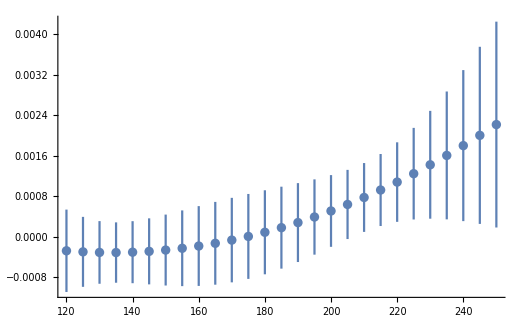

```mathematica
Show[Plot[{Kappa4T[T,0,0,0],Kappa4T[T,0,0,b],Kappa4T[T,0,a,b]},{T,10,200}], ErrorListPlot[KappaLat[[All,{1,4,5}]]],PlotRange->All]
```

## Plots

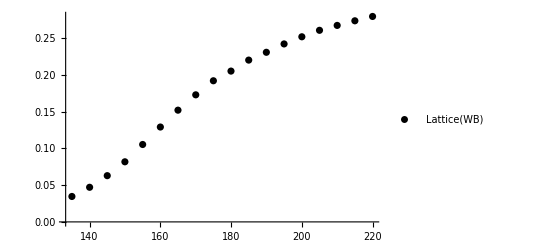

```mathematica
Lat=ErrorListPlot[chiss[[All,{1,2,3}]],PlotLegends->Placed[{"Lattice(WB)"},{0.2,0.6}],LabelStyle->{Black,Bold,25}, PlotStyle->Black]
```

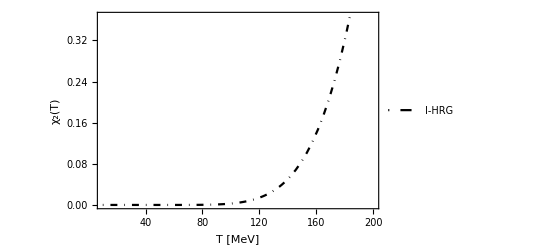

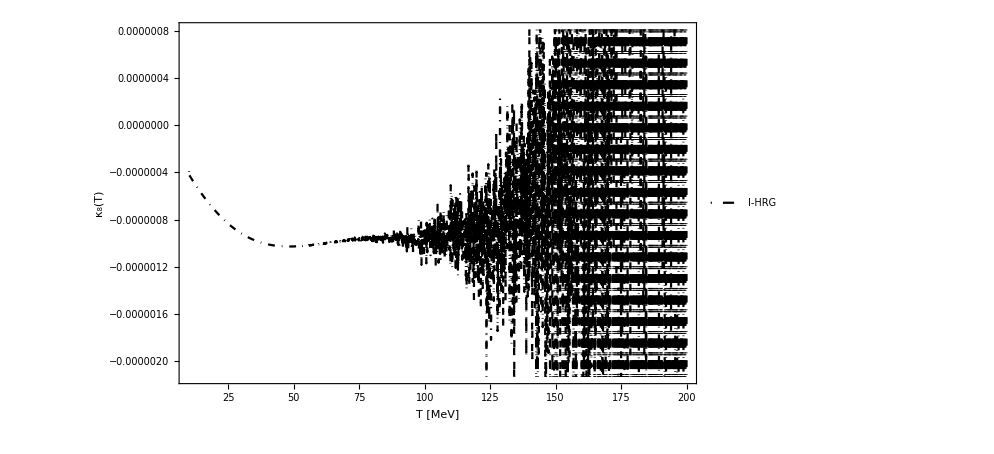

```mathematica
Id = Plot[{ch2hrgAA[T,0,0,0]},{T,10,200}, PlotStyle->{DotDashed,Black},PlotLegends->Placed[{"I-HRG"},{0.17,0.9}],FrameLabel->{"T [MeV]","χ_2(T)"},LabelStyle->{Black,Bold,25}, Frame->True]
```

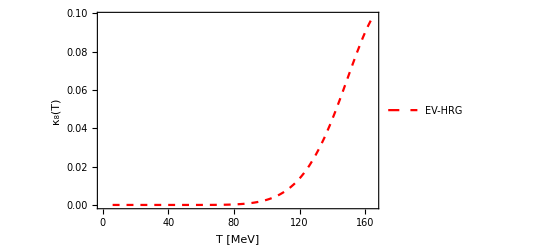

```mathematica
Exl = Plot[{ch2hrgAA[T,0,0,b]},{T,6,165}, PlotStyle->{Dashed,Red},PlotLegends->Placed[{"EV-HRG"},{0.18,0.8}],FrameLabel->{"T [MeV]","κ_8(T)"},LabelStyle->{Black,Bold,25}, Frame->True, PlotRange->Automatic]
```

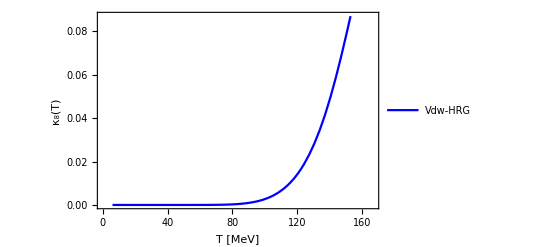

```mathematica
Vdw = Plot[{ch2hrgAA[T,0,a,b]},{T,6,167}, PlotStyle->{Bold,Blue, Large},PlotLegends->Placed[{"Vdw-HRG"},{0.2,0.7}],FrameLabel->{"T [MeV]","κ_8(T)"},LabelStyle->{Black,Bold,25}, Frame->True, PlotRange->Automatic]
```

```mathematica
Show[Id,Exl,Vdw,LabelStyle->{Black,Bold,25},PlotRange->{{25,220},Automatic}]
```

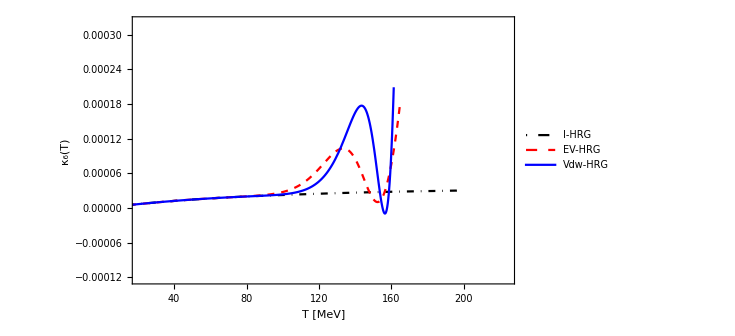

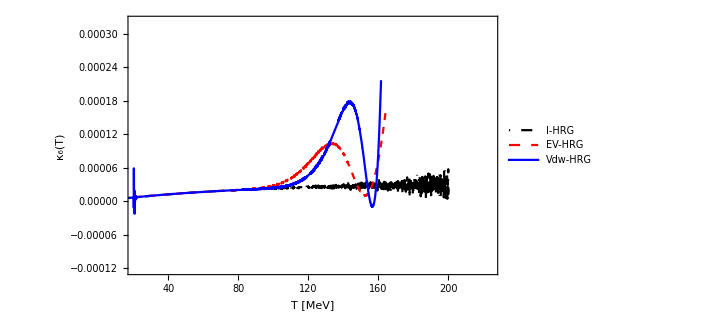

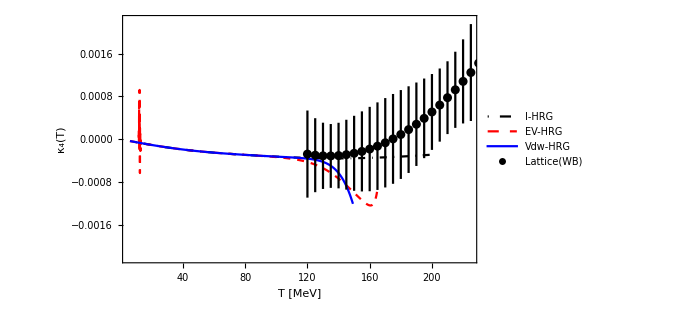

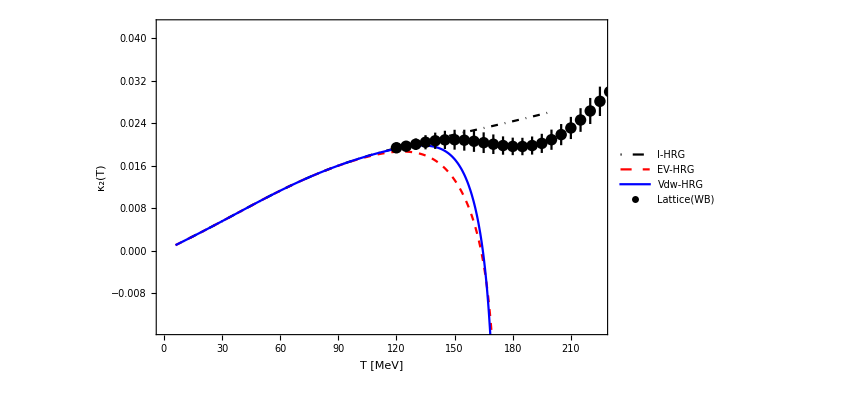

```mathematica
Chi2shift0[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b]
Chi2shift2[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T *(1+Kappa2[T,0,a,b]*(muB/T)^2 ),0,a,b];
Chi2shift4[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T *(1+Kappa2[T,0,a,b]*(muB/T)^2 +Kappa4[T,0,a,b]*(muB/T)^4),0,a,b];
Chi2shift6[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T *(1+Kappa2[T,0,a,b]*(muB/T)^2 +Kappa4[T,0,a,b]*(muB/T)^4+Kappa6[T,0,a,b]*(muB/T)^6),0,a,b];
Chi2shift8[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T *(1+Kappa2[T,0,a,b]*(muB/T)^2 +Kappa4[T,0,a,b]*(muB/T)^4+Kappa6[T,0,a,b]*(muB/T)^6+Kappa8[T,0,a,b]*(muB/T)^8),0,a,b];

(*Taylor Expansion*)
(*TChi2shift1[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b];
TChi2shift3[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b]+1/(3!)*(muB/T)^3*ch4hrgAA[T ,0,a,b];
TChi2shift5[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b]+1/(3!)*(muB/T)^3*ch4hrgAA[T ,0,a,b]+1/(5!)*(muB/T)^5*ch6hrgAA[T ,0,a,b];
TChi2shift7[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b]+1/(3!)*(muB/T)^3*ch4hrgAA[T ,0,a,b]+1/(5!)*(muB/T)^5*ch6hrgAA[T ,0,a,b]+1/(7!)*(muB/T)^7*ch8hrgAA[T ,0,a,b];
TChi2shift9[T_,muB_,a_,b_]:= muB/T*ch2hrgAA[T ,0,a,b]+1/(3!)*(muB/T)^3*ch4hrgAA[T ,0,a,b]+1/(5!)*(muB/T)^5*ch6hrgAA[T ,0,a,b]+1/(7!)*(muB/T)^7*ch6hrgAA[T ,0,a,b]+1/(9!)*(muB/T)^9*ch8hrgAA[T ,0,a,b];
*)
```

```mathematica
Tm=140;
```

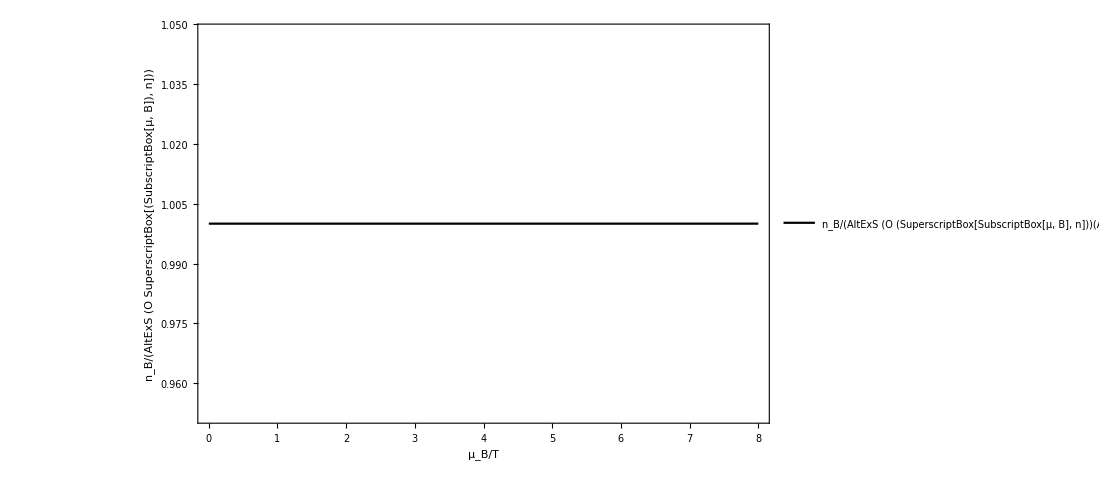

```mathematica
nful =Plot[{Bardenfull[Tm,n*Tm,a,b]/Bardenfull[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Bold,Black, Large},PlotLegends->Placed[{"n_B/(AltExS (O (SuperscriptBox[SubscriptBox[μ, B], n]))(AltExS)"},{0.2,0.7}],FrameLabel->{"μ_B/T"," n_B/(AltExS (O SuperscriptBox[(SubscriptBox[μ, B]), n])) "},LabelStyle->{Black,Bold,25}, Frame->True]
```

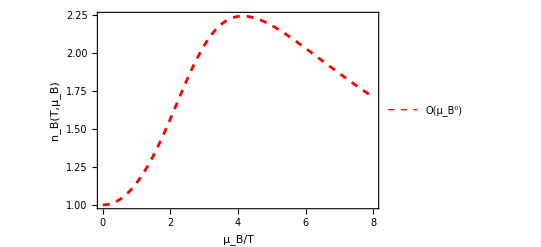

```mathematica
n0=Plot[{Bardenfull[Tm,n*Tm,a,b]/Chi2shift0[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Thickness[0.005],Dashed,Red},PlotLegends->Placed[{"O(μ_B^0)"},{0.18,0.8}],FrameLabel->{"μ_B/T "," n_B(T,μ_B)"},LabelStyle->{Black,Bold,25}, Frame->True]
```

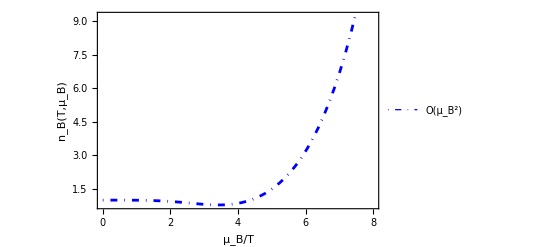

```mathematica
n2=Plot[{Bardenfull[Tm,n*Tm,a,b]/Chi2shift2[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Thickness[0.005],DotDashed,Blue},PlotLegends->Placed[{"O(μ_B^2)"},{0.18,0.8}],FrameLabel->{"μ_B/T"," n_B(T,μ_B)"},LabelStyle->{Black,Bold,25}, Frame->True]
```

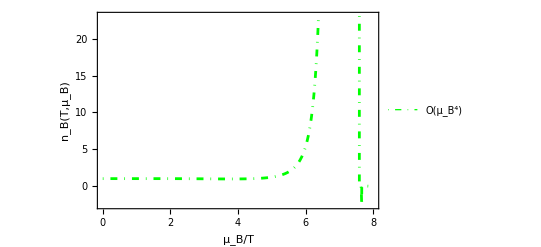

```mathematica
n4=Plot[{Bardenfull[Tm,n*Tm,a,b]/Chi2shift4[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Thickness[0.005],DotDashed,Green},PlotLegends->Placed[{"O(μ_B^4)"},{0.18,0.8}],FrameLabel->{"μ_B/T"," n_B(T,μ_B) "},LabelStyle->{Black,Bold,25}, Frame->True]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

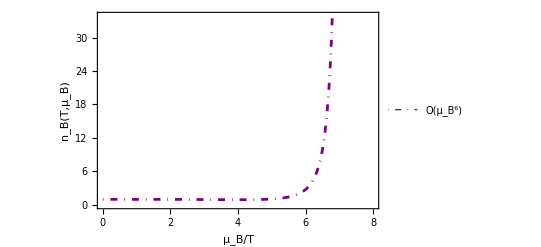

```mathematica
n6=Plot[{Bardenfull[Tm,n*Tm,a,b]/Chi2shift6[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Thickness[0.005],DotDashed,Purple},PlotLegends->Placed[{"O(μ_B^6)"},{0.18,0.8}],FrameLabel->{"μ_B/T"," n_B(T,μ_B) "},LabelStyle->{Black,Bold,25}, Frame->True]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

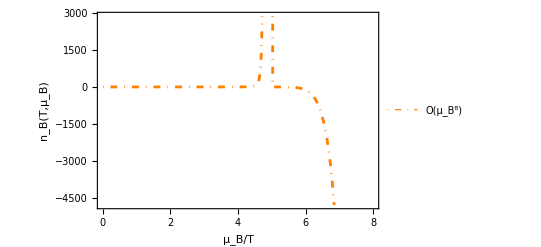

```mathematica
n8=Plot[{Bardenfull[Tm,n*Tm,a,b]/Chi2shift8[Tm,n*Tm,a,b]},{n,0,8}, PlotStyle->{Thickness[0.005],DotDashed,Orange},PlotLegends->Placed[{"O(μ_B^8)"},{0.18,0.8}],FrameLabel->{"μ_B/T"," n_B(T,μ_B) "},LabelStyle->{Black,Bold,25}, Frame->True]
```

```mathematica
Show[nful,n0,n2,n4,n6,n8, PlotRange->{{0,6},{0.5,3}}]
```

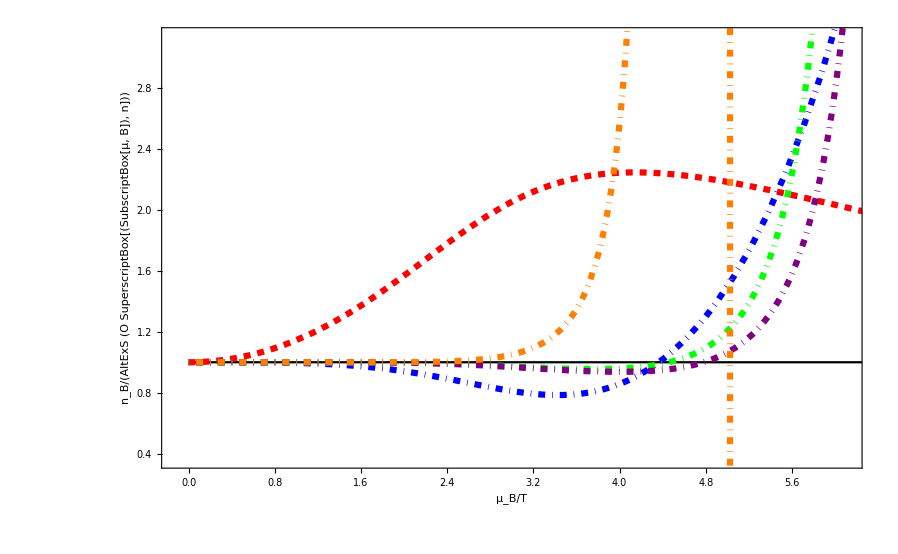

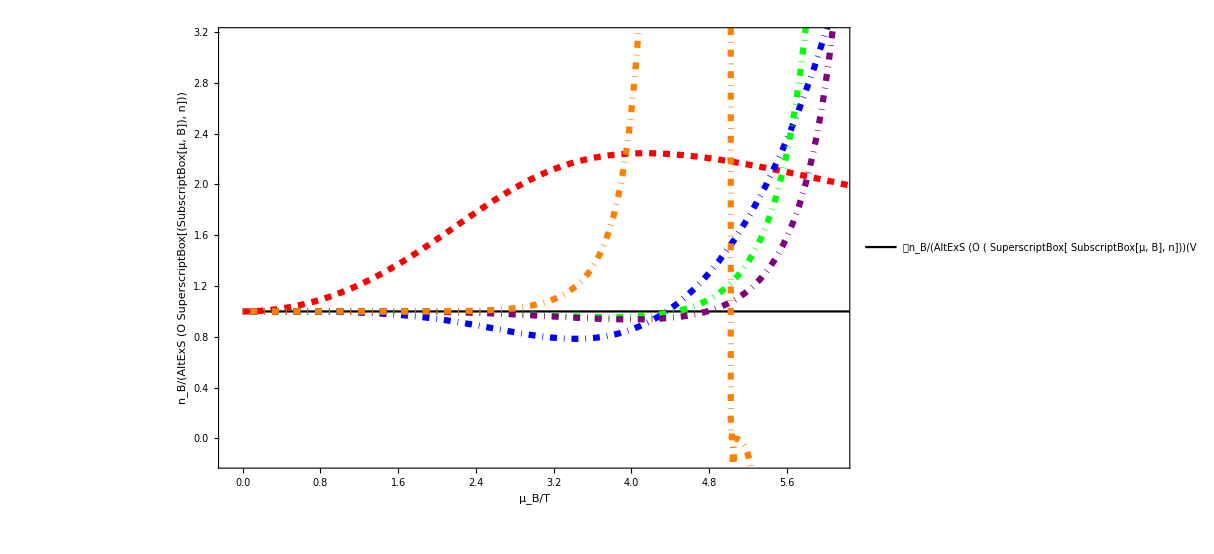

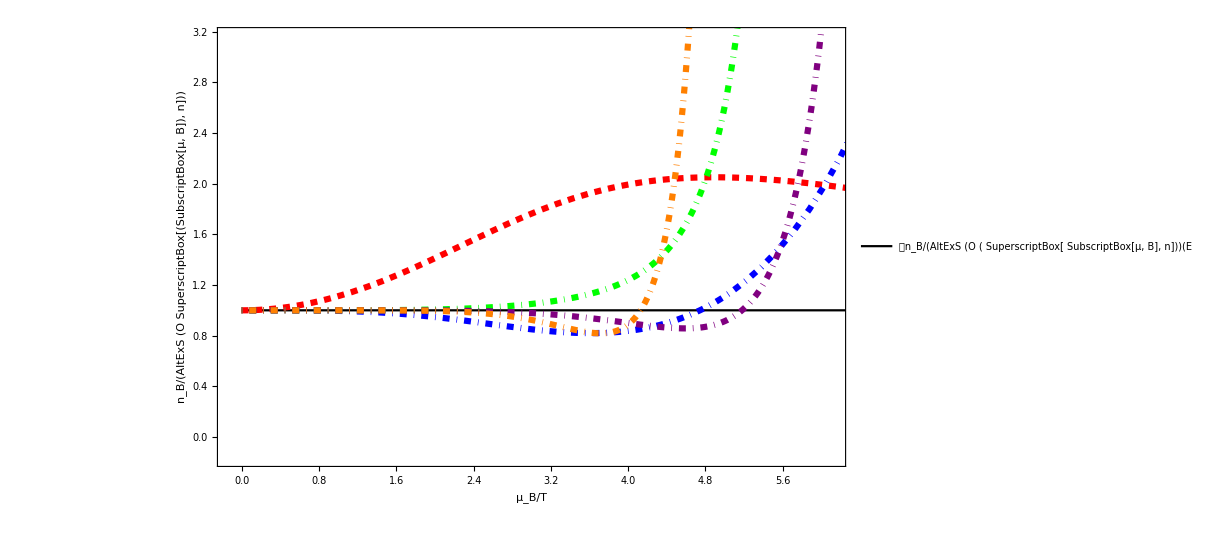

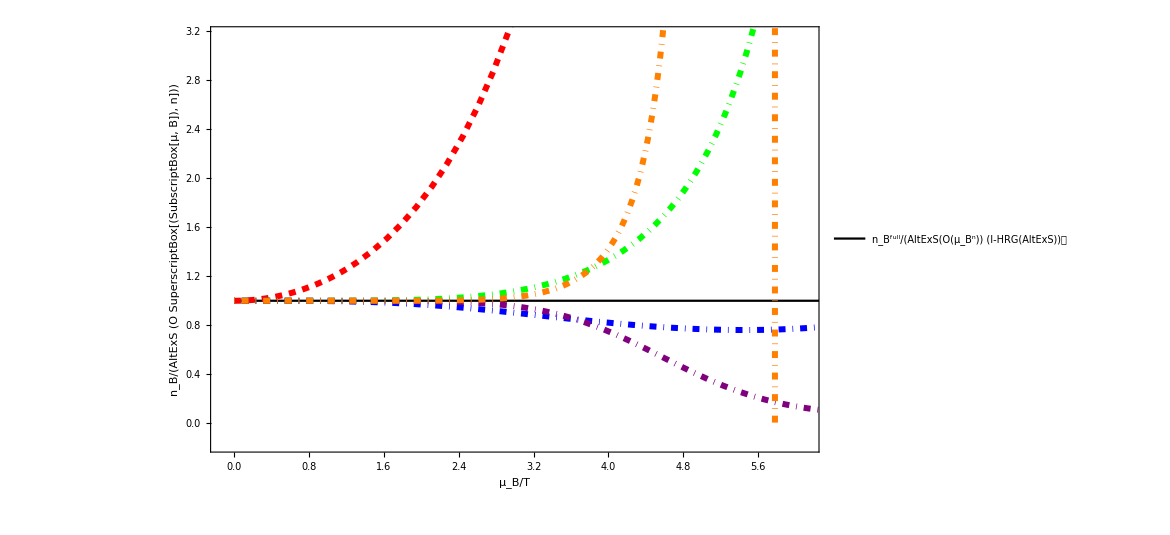

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

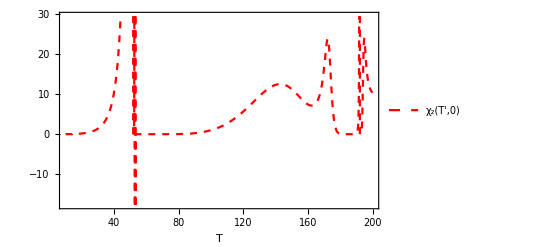

```mathematica
muBT = 500;
chi2T=Plot[{Chi2shift4[T,muBT,a,b]},{T,10,200}, PlotStyle->{Dashed,Red},PlotLegends->Placed[{"χ_2(T',0)"},{0.18,0.8}],FrameLabel->{"T "," "},LabelStyle->{Black,Bold,25}, Frame->True]
```

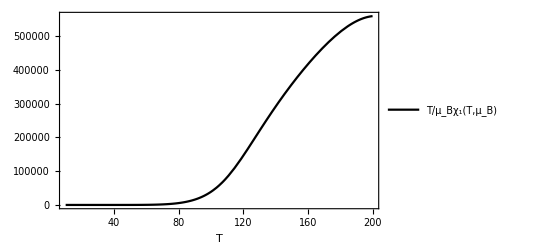

```mathematica
TmuBchi1 =Plot[{T/muBT nBDensity[T,muBT,a,b]},{T,10,200}, PlotStyle->{Bold,Black, Large},PlotLegends->Placed[{"T/μ_Bχ_1(T,μ_B)"},{0.2,0.7}],FrameLabel->{"T","  "},LabelStyle->{Black,Bold,25}, Frame->True, PlotRange->All]
```

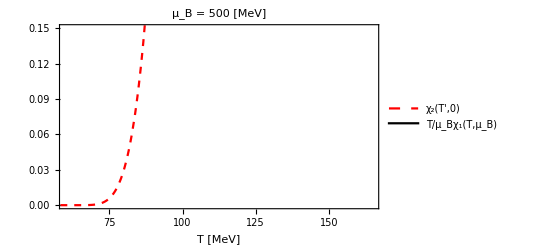

```mathematica
Show[chi2T,TmuBchi1, PlotLabel->"μ_B = 500 [MeV]",PlotRange->{{60,165},{0,0.15}}, FrameLabel->{"T [MeV]", " "}]
```

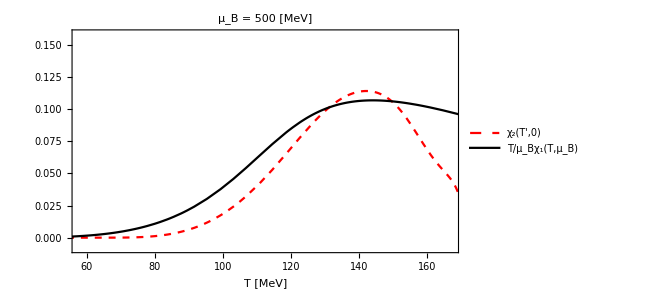

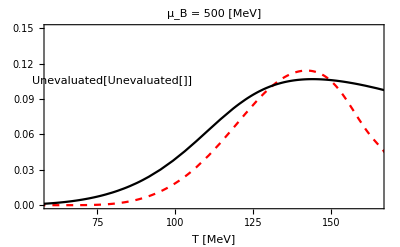

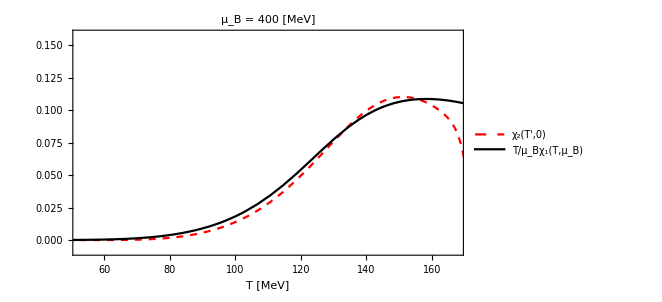

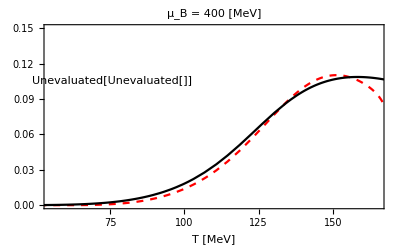

```mathematica
g[nB_]:=Log[bt*nB] -Log[1-bt*nB] + (bt*nB)/(1-bt*nB) - (2*at*nB)/T;

D[g[nB],{nB,1}]
```

1/nB+(bt^2 nB)/(1-bt nB)^2+(2 bt)/(1-bt nB)-(2 at)/T

```mathematica
ch2[T_,n_]:=1/nB[T,n]*[1/(1-bt*nB[T,n])^2-(2*at*nB[T,n])/T];
ch3[T_,n_]:=(1/nB[T,n])'[-(2 at nB[T,n])/T+1/(1-bt nB[T,n])^2] (-(2 at Derivative[0,1][nB][T,n])/T+(2 bt Derivative[0,1][nB][T,n])/(1-bt nB[T,n])^3)+(-(Derivative[0,1][nB][T,n])/nB[T,n]^2)[-(2 at nB[T,n])/T+1/(1-bt nB[T,n])^2]
```

```mathematica
D[ch2[T,n],n]
```

(1/nB[T,n])'[-(2 at nB[T,n])/T+1/(1-bt nB[T,n])^2] (-(2 at nB^(0,1)[T,n])/T+(2 bt nB^(0,1)[T,n])/(1-bt nB[T,n])^3)+(-(nB^(0,1)[T,n])/nB[T,n]^2)[-(2 at nB[T,n])/T+1/(1-bt nB[T,n])^2]

```mathematica
Sumpaclet:ref/Sum[D[g[nB],{nB,2}],{2,n}]
```

RefLink[Sum,paclet:ref/Sum][-1/nB^2+(2 bt^3 nB)/(1-bt nB)^3+(3 bt^2)/(1-bt nB)^2,{2,n}]

```mathematica
BellY[7,7,{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}]
```

x_1^7

```mathematica
f[T_,muB_]:=nBDensityt[T,muB]/T*(1/(1-bt*nBDensityt[T,muB])^2-(2*at*nBDensityt[T,muB])/T )^-1;
```

```mathematica
Simplify[D[f[T,muB],{muB,1}]]
```

(T (-1+bt nBDensityt[T,muB]) (-1+3 bt nBDensityt[T,muB]) nBDensityt^(0,1)[T,muB])/((T-2 at nBDensityt[T,muB]+4 at bt nBDensityt[T,muB]^2-2 at bt^2 nBDensityt[T,muB]^3)^2)

```mathematica
Simplify[D[f[T,muB],{muB,2}]]/.{Derivative[0,2][nBDensityt][T,muB]->(T^2 (-1+bt nBDensityt[T,muB]) (-1+3 bt nBDensityt[T,muB]) Derivative[0,1][nBDensityt][T,muB])/((T-2 at nBDensityt[T,muB]+4 at bt nBDensityt[T,muB]^2-2 at bt^2 nBDensityt[T,muB]^3)^2)}
```

(T ((T^2 (-1+bt nBDensityt[T,muB]) (-1+3 bt nBDensityt[T,muB]) (1-4 bt nBDensityt[T,muB]+3 bt^2 nBDensityt[T,muB]^2) nBDensityt^(0,1)[T,muB])/(T-2 at nBDensityt[T,muB]+4 at bt nBDensityt[T,muB]^2-2 at bt^2 nBDensityt[T,muB]^3)+(4 (at-bt T)+6 bt (-4 at+bt T) nBDensityt[T,muB]+60 at bt^2 nBDensityt[T,muB]^2-64 at bt^3 nBDensityt[T,muB]^3+24 at bt^4 nBDensityt[T,muB]^4) (nBDensityt^(0,1)[T,muB])^2))/(T-2 at nBDensityt[T,muB]+4 at bt nBDensityt[T,muB]^2-2 at bt^2 nBDensityt[T,muB]^3)^3